# Libra package examples

### Loading package

```mathematica
<<Libra`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

## Example #1: basic functionality

```mathematica
Quit
```

```mathematica
m="5×5 example matrix, depending on \!\(\*\nStyleBox[\"x\", \"TI\"]\) and \!\(\*\nStyleBox[\"ϵ\", \"TI\"]\)."
```

```mathematica
NewDSystem[ds1,x->m];
```

```mathematica
DSystemQ[ds1]
```

Note that only commands Transform[ds1,...], Factor[ds1], Simplify[ds1], Map[f,ds1,...] and a few others are dangerous in a sense that they actually modify the differential system, while VisTransformation, FuchsifyBlock, FactorOut only construct the transformation and thus are safe. 
But even the dangerous commands are safe because their effect can be undone with Undo[ds1]

First, we use visual tool VisTransformation to balance the matrix. Note that the option Highlighted→{…} is supposed to guide you through this process by highlighting tha buttons to be pressed, but it is extremely fragile. This is because the ordering of the eigenvectors, and even their choice (when there is a degeneracy) is not unique and may differ from Mathematica’s version to version. Therefore, rely on the common sense trying to press blue buttons on the left and red ones on the right as much as possible.

```mathematica
t=VisTransformation[ds1,x,ϵ,Log->True,Highlighted->{{11}⟷{22},{2,3,4,5}⟷{6,7,8,9},{11,12,13,14}⟷{16,17,18,19},{14}⟷{20},{20}⟷{15}}];
```

Now we apply the transformation found. 
Note that Libra knows that our system is wrt x, so there is nether need nor possibility to indicate this. So, we shall use the Transform[ds1,t].
You could get the same transformed matrix via Transform[ds1[x],t,x] (note that the first argument now is the matrix, not the differential system), but this will not change the history of ds1.
So, if m is matrix, use Transform[m,t,x] syntax for differential transformation and Transform[m,t] for similarity transformation Inverse[t].m.t. 
If, however, the first argument is the differential system, Transform[ds1,t]

```mathematica
ds1[x]===m
```

Before actually modifying the differential system, let us apply the transformation to a matrix.

```mathematica
m1=Transform[ds1[x],t,x]
```

The system has not changed:

```mathematica
ds1[x]===m
```

Now we apply the transformation the the system:

```mathematica
Transform[ds1,t];
```

The system has changed:

```mathematica
ds1[x]===m
```

The matrix in the rhs is equal to m1:

```mathematica
ds1[x]===m1
```

We can freely undo and redo transformations:

```mathematica
Undo[ds1];
ds1[x]===m
```

```mathematica
Redo[ds1];
ds1[x]===m1
```

```mathematica
Block[{μ=1,C},C[1]=1;C[_]=0;
t=FactorOut[ds1[x],x,ϵ,μ]]
```

```mathematica
Transform[ds1,t]
```

```mathematica
EFormQ[ds1[x],ϵ]
```

We may want to simplify the numerical coefficients a bit. A good idea is to diagonalized one of the matrix residues:

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[ds1[x]/ϵ,{x,0,-1}]]
```

```mathematica
Transform[ds1,t]
```

Although, the higher-order series coefficients are not guaranted to have rational eigenvalues, it worth trying:

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[ds1[x]/ϵ,{x,0,1}]]
```

```mathematica
Transform[ds1,t]
```

```mathematica
MatrixPlot[ds1[x]]
```

Finally, to get the overall transformation, we use the following command:

```mathematica
t=HistoryConsolidate[ds1];
```

```mathematica
t
```

Now we can check that the found transformation is correct.

First, we undo all transformations:

```mathematica
Undo[ds1,All]
```

Now we re-apply the overall tranformation. However, the command below will complain:

```mathematica
Transform[ds1,t]
```

Athough, the command above returns the transformed matrix, it had no effect on the actual differential system:

```mathematica
ds1[x]===m
```

This is made for safety: Undo and Redo simply modifies the pointer to the specific history entry (HistoryIndex[ds1]), while the history list (History[ds1]) remains intact. 
By default, dangerous commands can modify differential system only if HistoryIndex[ds1]===Length[History[ds1]], i.e., when the pointer points to the last entry in history list. Therefore has to explicitly chop off the history list by HistoryChop[ds1] before the transformation is possible.

```mathematica
Length@History[ds1]-HistoryIndex[ds1]
```

```mathematica
HistoryChop[ds1];
```

```mathematica
Length@History[ds1]-HistoryIndex[ds1]
```

Now we can apply the transformation:

```mathematica
Transform[ds1,t]
```

```mathematica
Quit
```

## Example #2: many blocks

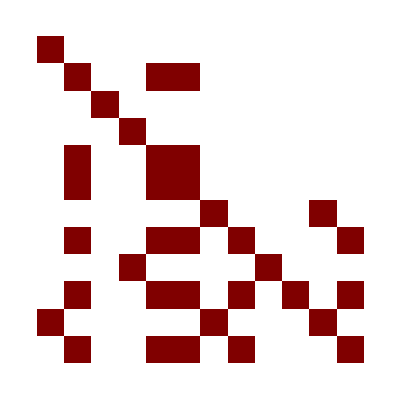
```mathematica
m=-Graphics-
```

```mathematica
NewDSystem[ds2,y->m];
```

Diagonal blocks indices are given by

```mathematica
inds=EntangledBlocksIndices[ds2]
```

Now we proceed block-by-block

## Diagonal blocks

#### 1

```mathematica
ii=inds[[1]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Log->True,Animate->{{1}⟷{2},{3}⟷{4}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=HistoryConsolidate[b]
```

Note that for 1×1 blocks we don’t need FactorOut as the eigenvalue of the matrix residue is simultaneously its only non-zero element.

```mathematica
Transform[ds2,t,ii];
```

```mathematica
EFormQ[ds2[[ii,ii]],ϵ]
```

#### 3

```mathematica
ii=inds[[2]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Log->True,Animate->{{1}⟷{2},{3}⟷{4}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

#### 4

```mathematica
ii=inds[[3]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{2}⟷{3},{2}⟷{3},{1}⟷{3},{2}⟷{3},{4}⟷{3},{4}⟷{3},{4}⟷{3}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

#### 2,5,6

```mathematica
ii=inds[[4]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{7}⟷{8},{17}⟷{8},{7}⟷{3},{13}⟷{9},{2}⟷{4},{8}⟷{10},{5}⟷{3},{11}⟷{9},{5}⟷{3},{11}⟷{9}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=FactorOut[b,y,ϵ,-1]/._C->1;
Transform[b,t];
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[y]/ϵ,{y,0,1}]]
Transform[b,t];
```

```mathematica
b[y]
```

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

#### 9

```mathematica
ii=inds[[5]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{1}⟷{2},{4}⟷{3}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

#### 7,11

```mathematica
ii=inds[[6]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{2}⟷{3},{6}⟷{7}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=FactorOut[b,y,ϵ,-1]/._C->1;
Transform[b,t];
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[y]/ϵ,{y,0,1}]]
Transform[b,t];
```

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

#### 8,12

```mathematica
ii=inds[[7]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{4}⟷{6},{12}⟷{8},{2}⟷{3},{10}⟷{11}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=FactorOut[b,y,ϵ,-1]/._C->1;
Transform[b,t];
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[y]/ϵ,{y,0,1}]]
Transform[b,t];
```

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

#### 10

```mathematica
ii=inds[[8]]
NewDSystem[b,ds2[[ii,ii]]]
```

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{1}⟷{2},{4}⟷{3}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

```mathematica
Transform[ds2,t,ii];
```

### Check

```mathematica
EFormQ[ds2[[#,#]],ϵ]&/@inds
```

## Saving intermediate results, quiting, and reloading

```mathematica
DumpSave["ds2",ds2];
```

```mathematica
Quit[]
```

```mathematica
Get["ds2"];
```

## Off-diagonal blocks

```mathematica
t=Fuchsify[ds2,y]
```

```mathematica
Transform[ds2,t];
```

```mathematica
FuchsianQ[ds2[y],y]
```

## Total factorization

```mathematica
t=FactorOut[ds2,y,ϵ,1]/._C->1;
```

```mathematica
t
```

```mathematica
Transform[ds2,t];
```

```mathematica
Factor[ds2]
```

```mathematica
EFormQ[ds2,ϵ]
```

```mathematica
Quit
```

## Example #3: using notations instead of variable change

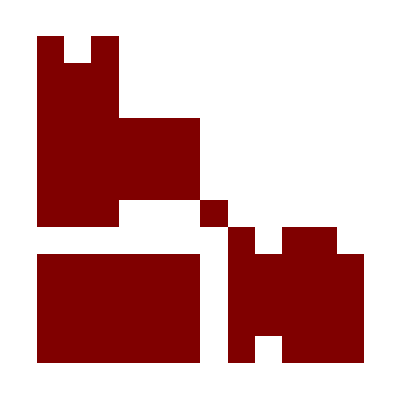
```mathematica
m=-Graphics-;(*m1=Factor[Get["Data/Mi"]/.d->4-2ϵ];*)
```

```mathematica
NewDSystem[ds3,s->m]
```

```mathematica
inds=EntangledBlocksIndices[m]
```

## Diagonal blocks

#### 1,2,3

```mathematica
ii=inds[[1]]
NewDSystem[b,ds3[[ii,ii]]]
```

```mathematica
b[]
```

While using visual tool below, we observe that there are ‘square root’  branching points at s=0 anf s=4. Therefore, we have to make the change of variable. But first we reduce the eigenvalues as much as possible.

```mathematica
t=VisTransformation[b,s,ϵ,Log->True,Highlighted->{{2}⟷{10},{9}⟷{6},{9}⟷{6},{8}⟷{6}}];
```

```mathematica
Transform[b,t];
```

As the number of ‘square root’ points, 2, is less than 4 (cf. arXiv:1707.07856, Section 4), we can use change of variable:

```mathematica
{{stoβ}}=Solve[√((s-4)/s)==β,s];stoβ
```

```mathematica
ChangeVar[b,stoβ,β];
```

NB: the second argument of VisTransformation below is the new variable β.

```mathematica
t=VisTransformation[b,β,ϵ,Log->True,Highlighted->{{6}⟷{12}}];
```

```mathematica
Transform[b,t];
```

```mathematica
t=FactorOut[b,β,ϵ,1/2]/._C->1;
```

```mathematica
Transform[b,t];
```

```mathematica
EFormQ[b,ϵ]
```

```mathematica
DenominatorsInfo[b,β]
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[β]/ϵ,{β,0,1}]]
```

```mathematica
Transform[b,t];b[β]
```

The overall transformation depends now on β rather than s:

```mathematica
t=HistoryConsolidate[b]
```

We can reduce the β appearance using QuolyMod and RuleToNotation functions:

```mathematica
βnotation=RuleToNotation[stoβ,β]
```

The above line should be undestood as “β is defined by the polynomial equation -4+s-s,β^2=0”. 
Now we  can ‘mod out’ any expression wrt the constraint -4+s-s,β^2=0.

```mathematica
t=QuolyMod[t,βnotation]
```

The result is necessarily the polynomial of β with degree one less that that of the constraint (i.e., deg=1 in our case).

Now, instead of changing variable in the whole matrix ds3, we introduce the corresponding notation:

```mathematica
AddNotation[ds3,βnotation];
```

```mathematica
Variables[ds3]
```

```mathematica
Notations[ds3]
```

NB: it is crucial to introduce notation before making transformation depending on it! Otherwise, Libra would assume β is some parameter independent of s and will calculate wrongly D[t,s] and, therefore, the whole transformation!

```mathematica
Transform[ds3,t,ii];
```

```mathematica
EFormQ[ds3[[ii,ii]],ϵ]
```

Note that the corresponding block now depends both on s and β. The dependence on the latter parameter is confined to be first-order polynomial:

```mathematica
ds3[[ii,ii]][s]
```

#### 4,5,6

```mathematica
ii=inds[[2]]
NewDSystem[b,ds3[[ii,ii]]];
```

```mathematica
Denominators[b]
```

Note that there are apparent (fake) singularities at zeros of 1-5 ϵ-s ϵ+4 ϵ^2+2 s ϵ^2. Since this denominator is linear in s, we can treat it on general ground, even with the visual tool below.

```mathematica
t=VisTransformation[b,s,ϵ,Log->True,Highlighted->{{6}⟷{7},{4}⟷{7},{3}⟷{5}}];
```

```mathematica
Transform[b,t];
```

```mathematica
Denominators[b]
```

```mathematica
t=FactorOut[b,s,ϵ,-2]/._C->1;
```

```mathematica
Transform[b,t];
```

```mathematica
EFormQ[b,ϵ]
```

```mathematica
DenominatorsInfo[b,s]
```

```mathematica
b[s]
```

In order to simplify the numerical coefficients a bit, we will ‘shake’ the system by diagonalizing residues:

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[s]/ϵ,{s,-1,-1}]];
Transform[b,t]
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[s]/ϵ,{s,0,-1}]];
Transform[b,t]
```

```mathematica
t=HistoryConsolidate[b]
```

```mathematica
Transform[ds3,t,ii];
```

```mathematica
EFormQ[ds3[[ii,ii]],ϵ]
```

```mathematica
ds3[[ii,ii]][s]
```

#### 7

```mathematica
ii=inds[[3]]
NewDSystem[b,ds3[[ii,ii]]];
```

```mathematica
Denominators[b]
```

```mathematica
t=VisTransformation[b,s,ϵ,Animate->{{1}⟷{2}}];
```

```mathematica
Transform[b,t];
```

```mathematica
Denominators[b]
```

```mathematica
b[]
```

```mathematica
t=HistoryConsolidate[b]
```

```mathematica
Transform[ds3,t,ii];
```

```mathematica
EFormQ[ds3[[ii,ii]],ϵ]
```

#### 8,9,10,11,12

```mathematica
ii=inds[[4]]
NewDSystem[b,ds3[[ii,ii]]];
```

```mathematica
Denominators[b]
```

Using visual tool, we see the ‘square root’ branching points at s=±2i. Again we first reduce to some extent other singular points.

```mathematica
t=VisTransformation[b,s,ϵ,Log->True,Animate->{{21}⟷{6},{3,4,5}⟷{16,17,18}}];
```

```mathematica
Transform[b,t];
```

```mathematica
Denominators[b]
```

We could have used the variable change √((s+2i)/(s-2i)), similar to what we have had previously. But that would potentially introduce imaginary unit in the matrix.
Here we choose another variable change, which also has square root branching points at s=±2i.

```mathematica
{{stoξ}}=Solve[√(4+s^2)-s==2ξ,s]
```

```mathematica
ChangeVar[b,stoξ,ξ];Factor[b]
```

A special care is needed when the singular points belong to algebraic extension of ℚ. The reason is that those algebraic extensions may unnecessarily appear in the final matrix. In particular, in our present example we have 2i, the root of s^2+4=0, and we would prefer that it does not appear in the transformation and in the final matrix.
Libra has special tools for treating irreducible denominators, but here we will apply a poor man approach by choosing the balances in a ‘symmetric way’ and hoping that the overall transformation will not depend on i.

```mathematica
t=VisTransformation[b,ξ,ϵ,Log->True,Animate->{{5}⟷{15},{25}⟷{20},{1}⟷{15},{21}⟷{20},{1}⟷{15},{21}⟷{20}}];
```

Let us check if we are lucky and t is real:

```mathematica
t=ExpandNumerator@ExpandDenominator@Factor[t];
FreeQ[t,_Complex]
```

Yes, we are. So we apply the transformation:

```mathematica
Transform[b,t];
```

```mathematica
t=FactorOut[b,ξ,ϵ,-2]/._C->1;
```

```mathematica
Transform[b,t];
```

```mathematica
EFormQ[b,ϵ]
```

```mathematica
DenominatorsInfo[b,ξ]
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[ξ]/ϵ,{ξ,0,1}]];
Transform[b,t]
```

```mathematica
ξnotation=RuleToNotation[stoξ,ξ]
```

```mathematica
t=QuolyMod[HistoryConsolidate[b],ξnotation]
```

```mathematica
AddNotation[ds3,ξnotation];
Variables[ds3]
Notations[ds3]
```

```mathematica
Transform[ds3,t,ii];
```

```mathematica
t
```

```mathematica
EFormQ[ds3[[ii,ii]],ϵ]
```

### Check&Save

```mathematica
EFormQ[ds3[[#,#]],ϵ]&/@inds
```

```mathematica
DumpSave["Data/ds3.tmp",ds3];
```

## Off-diagonal blocks

```mathematica
Get["Data/ds3.tmp"]
```

```mathematica
obi=OffDiagonalBlocksIndices[ds3]
```

Note that it is essential that off-diagonal blocks are reduced in a special order, e.g., as they appear in OffDiagonalBlocksIndices[ds3]

### {4,5,6},{1,2,3}

```mathematica
block=obi[[1]]
```

```mathematica
t=FuchsifyBlock[ds3,s,block];
```

```mathematica
Transform[ds3,t,Flatten[block]];
```

```mathematica
FuchsianQ[ds3[[Flatten[block],Flatten[block]]],s]
```

### {7},{1,2,3}

```mathematica
block=obi[[2]]
```

```mathematica
t=FuchsifyBlock[ds3,s,block];
```

```mathematica
Transform[ds3,t,Flatten[block]];
```

```mathematica
FuchsianQ[ds3[[Flatten[block],Flatten[block]]],s]
```

### {8,9,10,11,12},{4,5,6}

```mathematica
block=obi[[3]]
```

```mathematica
t=FuchsifyBlock[ds3,s,block];
```

```mathematica
Transform[ds3,t,Flatten[block]];
```

```mathematica
FuchsianQ[ds3[[Flatten[block],Flatten[block]]],s]
```

### {8,9,10,11,12},{1,2,3}: collision of notations, proceeding manually

NB: Don’t rely on FuchsianQ when there are notations!

```mathematica
block=obi[[4]]
```

As of the time this tutorial is written, FuchsifyBlock may treat at most one notation. Since block {1,2,3}×{1,2,3} uses β and {8,9,10,11,12}×{8,9,10,11,12} uses ξ, in the off-diagonalblock both of them appear. Therefore, FuchsifyBlock fails:

```mathematica
t=FuchsifyBlock[ds3,s,block]
```

Therefore, we have to do it in a semi-manual way. We start by copying the corresponding submatrix. 
Do not foget to copy notations!

```mathematica
NewDSystem[b,ds3[[Flatten@Reverse@block,Flatten@Reverse@block]]];
AddNotation[b,#]&/@(Notations[ds3]/.Association->List);
```

Both β and ξ enter the matrix at most to the first power since the corresponding polynomials are quadratic:

```mathematica
Notations[b]
```

We first examine denominators:

```mathematica
DenominatorsInfo[b,s]
```

#### Denominator s

It is temptful to start with s=0. However, there is a problem here. Note that β→∞ when s→0. Therefore, when we fuchsify other points (which requires β in the numerator), we can spoil the behaviour at s=0. The same thing relates to s=∞ and ξ (see below).

#### Denominator 4+s^2

Nothing especially bad happens with β and ξ:

```mathematica
Solve[#==0]&/@(Values@Notations[b]/.s->-2I)
```

```mathematica
den=4+s^2;(*denominator*)
```

```mathematica
r=2;(*Poincare rank*)
```

Since den is quadratic in s, we allow for the first power of s also:

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,2,2,2}];
t[[{4,5,6,7,8},{1,2,3}]]=(((cs.{1,β}).{1,ξ}).{1,s})/den^r;
```

We could have applied the transformation to the whole matrix, but it would take a lot of time. In this case even the principal part is too complicated for transformation, so we pick out only those terms which enter the equations:
Diagonal blocks  ∝(4+s^2)^-1
Off-diagonal block  ∝(4+s^2)^(-1-r)

```mathematica
Pp=SeriesCoefficientMod[b[s],{s->den,-r-1}]/den^(r+1);
(Pp[[#,#] ]=SeriesCoefficientMod[b[[#,#]][s],{s->den,-1}]/den;)&/@EntangledBlocksIndices[b];
```

```mathematica
Ppnew=Transform[Pp,t,{s,Notations[b]},UseFermat->True];
```

```mathematica
eqs=Flatten[CoefficientList[SeriesCoefficientMod[Ppnew,{s->den,-r-1}],{β,ξ,s}]];
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]];
```

```mathematica
t=t/.csrules;
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

```mathematica
Transform[b,t];
```

```mathematica
DenominatorsInfo[b,s]
```

Now we repeat with r=1

```mathematica
r=1;(*Poincare rank*)
```

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,2,2,2}];
t[[{4,5,6,7,8},{1,2,3}]]=(((cs.{1,β}).{1,ξ}).{1,s})/den^r;
```

```mathematica
Pp=SeriesCoefficientMod[b[s],{s->den,-r-1}]/den^(r+1);
(Pp[[#,#] ]=SeriesCoefficientMod[b[[#,#]][s],{s->den,-1}]/den;)&/@EntangledBlocksIndices[b];
```

```mathematica
Ppnew=Transform[Pp,t,{s,Notations[b]/.Association->List}];
```

```mathematica
eqs=Flatten[CoefficientList[SeriesCoefficientMod[Ppnew,{s->den,-r-1}],{β,ξ,s}]];
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]];
```

```mathematica
t=t/.csrules;
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

```mathematica
Transform[b,t];
```

```mathematica
DenominatorsInfo[b,s]
```

So, we have obtained the Fuchsian form at s=±2i. Good time to save

```mathematica
DumpSave["Data/b.tmp",b];
```

#### s→∞

The limit s→∞ should be analyzed with care. Notation β goes to 1, but ξ might go to ∞ too. Threfore, we shoud better eliminate terms of the form ξ/s.

However, there are no such terms:

```mathematica
Factor@Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

#### Denominator s

We start from s=0. The idea is the following: we make a template matrix, apply the transformation and solve for the coefficients to reduce the pole order.

```mathematica
EntangledBlocksIndices[b]
```

```mathematica
den=s;(*denominator*)
```

```mathematica
r=1;(*Poincare rank*)
```

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,2,2}];
t[[{4,5,6,7,8},{1,2,3}]]=((cs.{1,β}).{1,ξ})/den^r
```

We could have applied the transformation to the whole matrix, but it would take a lot of time. So we apply it to the principal part of expansion:

```mathematica
Pp=Sum[SeriesCoefficientMod[b[s],{s->den,k}] den^k,{k,-r-1,-1}];
```

Normal[Series[b[s],{s,0,-1}]] would have the same effect:

```mathematica
Factor[Pp-Normal[Series[b[s],{s,0,-1}]]]
```

```mathematica
eqs=Flatten[CoefficientList[SeriesCoefficientMod[Transform[Pp,t,{s,Notations[b]/.Association->List}],{s->den,-r-1}],{β,ξ}]];
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]];
```

```mathematica
t=t/.csrules;
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

```mathematica
Transform[b,t];
```

```mathematica
DenominatorsInfo[b,s]
```

We might have thought that the system b is Fuchsian at s=0 now, but there is a subtle point here: when s goes to zero  β goes to infinity. Therefore, terms of the form β/s are not Fuchsian.  Thus, we eliminate them. Basically, this kind of complications resist the fully automated approach.

One way to see this is to examine our notations at s=0:

```mathematica
Simplify[Values@Notations[b]/.s->0]
```

We see that the first notation corresponds to the equation -4==0, which has no solutions.

```mathematica
r=0;(*Formal Poincare rank*)
```

```mathematica
Factor@Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

Note that ξ might go to -s or to 0 when s goes to ∞. Therefore, not to spoil infinity, we can not use ξ upstairs

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,1}];
t[[{4,5,6,7,8},{1,2,3}]]=(cs*β).{1(*,ξ (*not allowed*)*)}
```

We could have applied the transformation to the whole matrix, but it would take a lot of time. So we apply it to the principal part of expansion.
NB: When s→0, β grows as s^(-1/2), so the terms β s^0∝s^(-1/2) are irrelevant (smaller than s^-1).

```mathematica
Pp=Sum[SeriesCoefficientMod[b[s],{s->den,k}] den^k,{k,-r-1,-1}];
```

Normal[Series[b[s],{s,0,-1}]] would have the same effect:

```mathematica
Factor[Pp-Normal[Series[b[s],{s,0,-1}]]]
```

Indeed, there are dangerous terms:

```mathematica
Factor[Coefficient[Pp,β]]
```

```mathematica
eqs=Flatten[CoefficientList[Coefficient[SeriesCoefficientMod[Transform[Pp,t,{s,Notations[b]/.Association->List}],{s->den,-r-1}],β],ξ]];
```

The fact that the equations are compatible comes out as a surprise:

```mathematica
Length[eqs]
Length[Flatten@cs]
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]]
```

```mathematica
t=Factor[t/.csrules];
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

Application will take some time:

```mathematica
Transform[b,t];
```

```mathematica
DenominatorsInfo[b,s]
```

Let us check if β is absent in s^-1 terms:

```mathematica
Coefficient[SeriesCoefficientMod[b[s],{s->den,-1}],β]
```

Let us check that we have not spoiled behaviour at ∞

```mathematica
Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

So, we have obtained the Fuchsian form at s=1. Good time to save

```mathematica
DumpSave["Data/b.tmp",b];
```

#### β→∞,ξ→∞

```mathematica
Get["Data/b.tmp"];
```

One might get an impression that we are done, but we should also consider the points where ξ and/or β go to ∞. Since ξ→∞ implies s→∞, and β→∞ implies s→0, we seem to be done.

#### Consolidating and applying

```mathematica
DenominatorsInfo[b,s]
```

```mathematica
t=HistoryConsolidate[b];
```

```mathematica
MatrixPlot[t]
```

Now we apply the transformation to ds3

NB: when creating the matrix b, we used Flatten@Reverse@block to have a familiar lower-triangular form (pay attention to Reverse). Therefore, we use the same when applying the overall transformation:

```mathematica
Transform[ds3,t,Flatten@Reverse@block];
```

```mathematica
DenominatorsInfo[ds3[[Flatten[block],Flatten[block]]],s]
```

```mathematica
Coefficient[SeriesCoefficient[ds3[[Flatten[block],Flatten[block]]][s],{s,0,-1}],β]
```

Let us check that we have not spoiled behaviour at ∞

```mathematica
Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

### Saving

```mathematica
DumpSave["Data/ds3.tmp1",ds3]
```

## Overall factorization

Since we have notations, it is not safe to use FactorOut. It is better to rely on the approach which also works for multivariate setup: sampling and factoring out dependence.

Ok, so we get samples in a few points . But we have to substitute notations

```mathematica
Get["Data/ds3.tmp1"]
```

```mathematica
βξcoefs=Coefficient[Coefficient[ds3[s],β,#1],ξ,#2]&@@@{{0,0},{0,1},{1,0},{1,1}};
```

```mathematica
samples=Flatten[βξcoefs/.({s->#}&/@RandomInteger[{5,30},3]),1];
```

There should be a transformation which eliminates ϵ from samples/ϵ, and we can search for it useing FactorDependence:

```mathematica
Variables[samples]
```

```mathematica
t=FactorDependence[samples/ϵ,ϵ,-3]/._C->1;Factor[Det[t]]
```

```mathematica
Transform[ds3,t];
```

```mathematica
EFormQ[ds3,ϵ]
```

```mathematica
Unprotect[ds3];Save["Data/ds3.res",ds3];
```

```mathematica
Quit[]
```

## Check

```mathematica
Get["Data/ds3.res"];
ds3[s]
```

```mathematica
Notations[ds3]
```

```mathematica
T=HistoryConsolidate[ds3];
```

```mathematica
Put[{T,Notations[ds3]},"Data/ds3Transformation&Notations"]
```

## Example #4: Irreducible and ugly denominators.

```mathematica
Quit
```

```mathematica
m="3×3 block with ugly denominator";
```

```mathematica
NewDSystem[ds4,z->m]
```

```mathematica
Denominators[ds4]
```

The last denominator is ugly: it depends both on z and ϵ. It should be possible to eliminate it.

### Getting rid of ugly denominator

```mathematica
den=Collect[Denominators[ds4][[-1]],z,Factor]
```

We need mod versions of SeriesCoefficient and similar function. For example, we can start with determining the order of poles

```mathematica
LeadingOrderMod[ds4[z],z->den]
```

Ok, this is a simple pole. Let us find the eigenvalues of matrix residues:

```mathematica
EValuesMod[SeriesCoefficientMod[ds4[z],{z->den,-1}],z->den]
```

From now on, to avoid keystrokes, we will use NotationsBlock to indicate which polynomial is use  to mod out. For exmaple, the above commands can be replaced with

```mathematica
NotationsBlock[{z->den},
Print@LeadingOrderMod[ds4[z],z];
Print@EValuesMod[SeriesCoefficientMod[ds4[z],{z,-1}],z];
]
```

Now, let us find the “eigenvector”, corresponding to nonzero eigenvalue. It should be the first one:

```mathematica
NotationsBlock[{z->den},
vs=ESpaceMod[Transpose@SeriesCoefficientMod[ds4[z],{z,-1}],z][[{1}]]
]
```

It happened so that this vector does depend on z, but in general, it will be the (n-1)-th order polynomial in z, where n is the degree of den. So, we proceed further as if vs depended on z .

The idea is to balance the ugly denominator with ∞, perhaps, at the expense of worsening the system’s properties at ∞. Leter on we will fix these properties by applying further transformations. However, we’d better do our best not to spoil the properties to much, otherwise, we can get stuck due to computational problems (e.g., time and/or memory restriction). For example, we find here  an appropriate subspace for the residue at z=0:

```mathematica
us=GetSubspaces[ds4[z],{z,0},ϵ][[2]]
```

GetSubspaces returns the list of bases for invariant subspaces. We take the second subspace which has appropriate dimension 1 and simple form of basis vector.
Although, it takes time to understand the format of GetSubspaces output, this procedure is almost inavoidable for complicated systems.

Now we cook up a projector and the corresponding balance

```mathematica
P=ProjectorMod[us,vs,z->den];
t=IdentityMatrix[Length@ds4]-P+P den/z;
```

Note that den is of 4-th degree, so the transformation t defined above is singular at zeros of den, at z=0 and at z=∞. Applying this transformation, we are likely to increase Poincare rank at z=∞ by 3 (=Exponent[den/z,z]). Since we have carefully chosen us, the Poincare rank at z=0 should not increase.

Before the transformation:

```mathematica
PoincareRank[ds4,{z,#}]&/@{0,∞}
```

Transform:

```mathematica
Transform[ds4,t];
```

After the transformation:

```mathematica
PoincareRank[ds4,{z,#}]&/@{0,∞}
```

Ok, the Poincare rank has increased by one at z=∞. 
But now we don’t have the ugly denominator:

```mathematica
Denominators[ds4]
```

### Irreducible denominator

The denominator 1+z^2 can be factorized as (z+I)(z-I), but thsi factorization will leave, in general, the complex numbers in the transformation and in the resulting matrix. Let us show, for the sake of completeness, how to treat 1+z^2 as irreducible denominator. Basically, we follow the same path as for ugly denominator

```mathematica
den=Collect[Denominators[ds4][[-1]],z,Factor]
```

```mathematica
NotationsBlock[{z->den},
Print@LeadingOrderMod[ds4[z],z];
Print@EValuesMod[SeriesCoefficientMod[ds4[z],{z,-1}],z];
]
```

Now, let us find the two “eigenvectors”, corresponding to nonzero eigenvalues. It should be the two first ones:

```mathematica
NotationsBlock[{z->den},
vs=ESpaceMod[Transpose@SeriesCoefficientMod[ds4[z],{z,-1}],z][[{1,2}]]
]
```

Let’s again respect 0

```mathematica
us=GetSubspaces[ds4[z],{z,0},ϵ][[{1,2}]]
```

It is two one-dimensional subspaces, so we just joint the bases:

```mathematica
us=Join@@us
```

Now we cook up a projector and the corresponding balance

```mathematica
P=ProjectorMod[us,vs,z->den];
t=IdentityMatrix[Length@ds4]-P+P den/z;
```

```mathematica
Transform[ds4,t];
```

```mathematica
PoincareRank[ds4,{z,#}]&/@{0,∞}
```

```mathematica
Denominators[ds4]
```

Ok, we got rid of the denomiantor 1+z^2

### Other singularities

```mathematica
t=VisTransformation[ds4,z,ϵ,Animate->{{5}⟷{13},{13}⟷{1},{13}⟷{7},{6}⟷{13},{5}⟷{1},{11}⟷{7}}];
```

```mathematica
Transform[ds4,t]
```

### Factoring out ϵ

```mathematica
t=FactorOut[ds4,z,ϵ,1]/._C->1;Factor@Det[t]
```

```mathematica
Transform[ds4,t]
```

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[ds4[z]/ϵ,{z,0,-1}]]
```

```mathematica
Transform[ds4,t]
```

## Example #5: two variables

```mathematica
Quit
```

Here we create the differential systems wrt x and y.

```mathematica
my="16x16 matrix \!\(\*SubscriptBox[\(M\), \(y\)]\) in \!\(\*SubscriptBox[\(∂\), \(y\)]\)J=\!\(\*SubscriptBox[\(M\), \(y\)]\)J";
mx="16x16 matrix \!\(\*SubscriptBox[\(M\), \(x\)]\) in \!\(\*SubscriptBox[\(∂\), \(x\)]\)J=\!\(\*SubscriptBox[\(M\), \(x\)]\)J";
```

Let us check the integrability conditions:

```mathematica
Factor[D[mx,y]-D[my,x]+mx.my-my.mx]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
NewDSystem[ds5,{x->mx,y->my}];
```

```mathematica
inds=EntangledBlocksIndices[ds5]
```

{{1},{2},{3},{4},{5,6},{7,8},{9},{10,11},{12},{13},{14},{15},{16}}

### Diagonal blocks

#### All 1x1 blocks

All 1x1 blocks can be trivially reduced to ϵ-form. Let us first elaborate on ds5[[1,1]]
The idea is to ‘integrate out’ the ϵ^0 term.

From now on we will put ϵ=0 when finding the transformation. First, note that due to integrability condition we have ∂_y (M_x)_11=∂_x (M_y)_11:

```mathematica
Factor[D[ds5[[1,1]][x]/.ϵ->0,y]-D[ds5[[1,1]][y]/.ϵ->0,x]]
```

0

Therefore, there exists M_11, such that (M_x)_11=∂_x M_11 and (M_y)_11=∂_y M_11.  We first use M_11=c(y)+∫(dx(M_x))_11, where c(y) is an unfixed function of y.

```mathematica
M11=Integrate[ds5[[1,1]][x]/.ϵ->0,x]
```

y (-Log[x]/y+Log[x-y]/y+Log[1-x y]/y)

In order to fix c(y), we use c(y)=M_11-∫(dx(M_x))_11=∫dy[∂_y M_11-∂_y ∫(dx(M_x))_11]=∫dy[(M_y)_11-∂_y ∫(dx(M_x))_11]

```mathematica
M11=Factor[M11+Integrate[Factor[ds5[[1,1]][y]-D[M11,y]]/.ϵ->0,y]]
```

-Log[x]+Log[x-y]-Log[y]+Log[1-x y]

Now the transformation is T_11=e^M_11:

```mathematica
t=FullSimplify[{{Exp[M11]}}]
```

{{-1/x-x+1/y+y}}

Let us check the found transformation:

```mathematica
Factor@Transform[ds5[[{1},{1}]][x],t,x]
Factor@Transform[ds5[[{1},{1}]][y],t,y]
```

{{-(2 (-1+x) (1+x) y ϵ)/(x (x-y) (-1+x y))}}

{{(2 x (-1+y) (1+y) ϵ)/((x-y) y (-1+x y))}}

Ok, indeed we found ϵ-form. No we do it in cycle for each 1x1 block:

```mathematica
onebyone =Select[inds,Length[#]==1&]
```

{{1},{2},{3},{4},{9},{12},{13},{14},{15},{16}}

```mathematica
t=IdentityMatrix[Length@ds5];
(Mii=Integrate[ds5[[#,#]][x]/.ϵ->0,x];Mii=Factor[Mii+Integrate[Factor[ds5[[#,#]][y]-D[Mii,y]]/.ϵ->0,y]];
t[[#,#]]=FullSimplify[Exp@Mii])&/@onebyone;
Diagonal[t]
```

{-1/x-x+1/y+y,1/y,y,1,1,1,1,1,1,1,1,1,x/(1-x^2),x/(1-x^2),x/(1-x^2),x^2/((-1+x^2)^2)}

Now we apply the transformation:

```mathematica
Transform[ds5,t];
```

Let’s check that we have indeed ϵ-form for all 1x1 diagonal blocks:

```mathematica
EFormQ[ds5[[#,#]],ϵ]&/@onebyone
```

{True,True,True,True,True,True,True,True,True,True}

#### {5,6}

```mathematica
ii=inds[[5]]
```

{5,6}

```mathematica
NewDSystem[b,ds5[[ii,ii]]]
```

History length for b is 1.

Successfully created differential system for 2 functions of x,y.

```mathematica
t=VisTransformation[b,x,ϵ,Animate->{{2}⟷{4},{6}⟷{12}}]
```

{{1,-ϵ/((-1+x) (1+x) (1-5 ϵ+6 ϵ^2))},{0,x/((-1+x) (1+x))}}

```mathematica
Transform[b,t];
```

History length for b is 2.

At this stage we have normalized matrix b_x. Now we do the same for b_y. However, we have to use only transformations which do not depend on x.

```mathematica
t=VisTransformation[b,y,ϵ,Log->True]
```

NB: option
	Highlighted→{}
will guide you through the same path,
 while option
	Animate→{}
will press the buttons for you ☺.

{{1,0},{0,1}}

b_y appeared to be already normalized.

Now we can factor our ϵ. We can use ,e.g. b_x:

```mathematica
t=FactorOut[b,x,ϵ,-1]/._C->1
```

{{1,0},{0,(-1+5 ϵ-6 ϵ^2)/(12 ϵ)}}

```mathematica
Transform[b,t];
```

History length for b is 3.

```mathematica
EFormQ[b,ϵ]
```

True

```mathematica
b[]
```

<|x→{{-((-1+2 x y-y^2) ϵ)/((x-y) (-1+x y)),ϵ/(6 (-1+x) x (1+x))},{-(24 ϵ)/x,((-1-3 x^2+6 x y+2 x^3 y-y^2-3 x^2 y^2) ϵ)/((-1+x) (1+x) (x-y) (-1+x y))}},y→{{(x (-1+y) (1+y) ϵ)/((x-y) y (-1+x y)),0},{0,(x (-1+y) (1+y) ϵ)/((x-y) y (-1+x y))}}|>

```mathematica
t=HistoryConsolidate[b];
```

```mathematica
Transform[ds5,t,ii];
```

```mathematica
EFormQ[ds5[[ii,ii]],ϵ]
```

True

#### {7,8}

```mathematica
ii=inds[[6]]
```

{7,8}

```mathematica
NewDSystem[b,ds5[[ii,ii]]]
```

History length for b is 1.

Successfully created differential system for 2 functions of x,y.

```mathematica
t=VisTransformation[b,x,ϵ,Animate->{{2}⟷{4},{6}⟷{12}}]
```

{{1,((1-y-x y+x^2 y) ϵ)/((-1+x) (1+x) (-1+2 ϵ) (-1+3 ϵ))},{0,x/((-1+x) (1+x))}}

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{2}⟷{9},{8}⟷{1}}]
```

{{1,(ϵ-y ϵ)/((-1+2 ϵ) (-1+3 ϵ))},{0,1}}

Check that t does not depend on x:

```mathematica
FreeQ[t,x]
```

True

```mathematica
Transform[b,t];
```

History length for b is 3.

Now we can factor our ϵ. We can use ,e.g. b_x:

```mathematica
t=FactorOut[b,x,ϵ,-1]/._C->1
```

{{1,0},{0,(-1+5 ϵ-6 ϵ^2)/(12 ϵ)}}

```mathematica
Transform[b,t];
```

History length for b is 4.

```mathematica
EFormQ[b,ϵ]
```

True

```mathematica
b[]
```

<|x→{{-ϵ/(x (-1+x y)),((-2 x+y+x^2 y) ϵ)/(12 (-1+x) (1+x) (-1+x y))},{(12 (-2 x+y+x^2 y) ϵ)/(x (x-y) (-1+x y)),-((3 x+x^3-y-7 x^2 y+2 x y^2+2 x^3 y^2) ϵ)/((-1+x) x (1+x) (x-y) (-1+x y))}},y→{{-ϵ/(y (-1+x y)),-(x ϵ)/(12 (-1+x y))},{-(12 (-1+x) (1+x) ϵ)/((x-y) (-1+x y)),((-x-y+2 x y^2) ϵ)/((x-y) y (-1+x y))}}|>

```mathematica
t=HistoryConsolidate[b];
```

```mathematica
Transform[ds5,t,ii];
```

```mathematica
EFormQ[ds5[[ii,ii]],ϵ]
```

True

#### {10,11}

```mathematica
ii=inds[[8]]
```

{10,11}

```mathematica
NewDSystem[b,ds5[[ii,ii]]]
```

History length for b is 1.

Successfully created differential system for 2 functions of x,y.

```mathematica
t=VisTransformation[b,x,ϵ,Animate->{{2}⟷{4},{6}⟷{12}}]
```

{{1,((-1-x+x^2+y) ϵ)/((-1+x) (1+x) y (-1+2 ϵ) (-1+3 ϵ))},{0,x/((-1+x) (1+x))}}

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{9}⟷{3},{2}⟷{7}}]
```

{{1,((-1+y) ϵ)/(y (-1+2 ϵ) (-1+3 ϵ))},{0,1}}

Check that t does not depend on x:

```mathematica
FreeQ[t,x]
```

True

```mathematica
Transform[b,t];
```

History length for b is 3.

Now we can factor our ϵ. We can use ,e.g. b_x:

```mathematica
t=FactorOut[b,x,ϵ,-1]/._C->1
```

{{1,0},{0,(-1+5 ϵ-6 ϵ^2)/(12 ϵ)}}

```mathematica
Transform[b,t];
```

History length for b is 4.

```mathematica
EFormQ[b,ϵ]
```

True

```mathematica
b[]
```

<|x→{{-(y ϵ)/(x (x-y)),((1+x^2-2 x y) ϵ)/(12 (-1+x) (1+x) (x-y))},{(12 y (1+x^2-2 x y) ϵ)/(x (x-y) (-1+x y)),-((2 x+2 x^3-y-7 x^2 y+3 x y^2+x^3 y^2) ϵ)/((-1+x) x (1+x) (x-y) (-1+x y))}},y→{{ϵ/(x-y),(x ϵ)/(12 (x-y) y)},{(12 (-1+x) (1+x) ϵ)/((x-y) (-1+x y)),((-2 x+y+x y^2) ϵ)/((x-y) y (-1+x y))}}|>

```mathematica
t=HistoryConsolidate[b];
```

```mathematica
Transform[ds5,t,ii];
```

```mathematica
EFormQ[ds5[[ii,ii]],ϵ]
```

True

#### Check diagonal blocks

```mathematica
EFormQ[ds5[[#,#]],ϵ]&/@inds
```

{True,True,True,True,True,True,True,True,True,True,True,True,True}

### Overall factorization

It appears that the differential system is already globally fuchsian at this point.

```mathematica
FuchsianQ[ds5,x]
FuchsianQ[ds5,y]
```

True

True

If it was not so, we would have run the following

```mathematica
t=Fuchsify[ds5,x];
Transform[ds5,t];
t=Fuchsify[ds5,y];
Transform[ds5,t];
```

Now we find the overall factorizing transformation. Although we don’t need to use sampling here, let us show this technique for the sake of completeness

```mathematica
samples=Join@@Table[{ds5[x],ds5[y]}/.{x->RandomInteger[30],y->RandomInteger[30]},{5}];
```

```mathematica
t=FactorDependence[samples/ϵ,ϵ,1]/._C->1
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,(2-9 ϵ+9 ϵ^2)/(2 ϵ (-1+2 ϵ)),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(-2+3 ϵ)/ϵ,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(-2+3 ϵ)/ϵ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(-2+3 ϵ)/ϵ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,(-2+3 ϵ)/ϵ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,(2-9 ϵ+9 ϵ^2)/(2 ϵ (-1+2 ϵ)),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,(-2+3 ϵ)/ϵ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,(-2+3 ϵ)/ϵ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,(2-9 ϵ+9 ϵ^2)/(2 ϵ (-1+2 ϵ)),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(-2+13 ϵ-27 ϵ^2+18 ϵ^3)/(2 ϵ^3),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,(-2+13 ϵ-27 ϵ^2+18 ϵ^3)/(2 ϵ^3),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,((-1+2 ϵ) (2-9 ϵ+9 ϵ^2))/(2 ϵ^3),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(-2+13 ϵ-27 ϵ^2+18 ϵ^3)/(2 ϵ^3)}}

```mathematica
Transform[ds5,t];
```

```mathematica
EFormQ[ds5,ϵ]
```

True